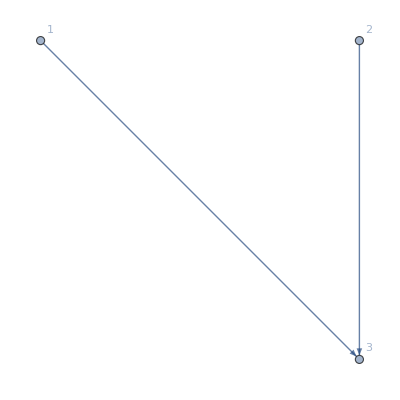

-Graphics3D-

```mathematica
f[x1_,x2_,w1_,w2_]:=w1*x1+w2*x2;
AdjacencyGraph[{{0,0,1},{0,0,1},{0,0,0}},VertexLabels->"Name"]
Plot3D[{f[x1,x2,-4.5,1.5],0},{x1,-1,1}, {x2,-1,1},PlotTheme->"Scientific", AxesLabel->Automatic]
```

```mathematica
Plot3D[{f[x1,x2,0.5,11.2]+10,f[x1,x2,-25.3,1.6]-2,f[x1,x2,2,-5.2]+7,0},{x1,-2,2}, {x2,-2,2},PlotTheme->"Scientific", AxesLabel->Automatic,ClippingStyle->None]
```

-Graphics3D-

```mathematica
g[x1_,x2_,w1_,w2_]:=f[x1,x2,w1,w2]/(1+Abs[f[x1,x2,w1,w2]]);
Plot3D[{g[x1,x2,0.5,0.2],0},{x1,-10,10}, {x2,-10,10},PlotTheme->"Scientific", AxesLabel->Automatic]
```

-Graphics3D-

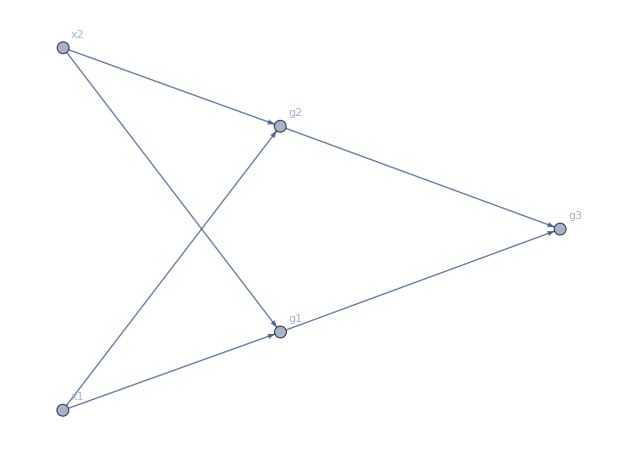
{(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0),-Graphics-}

```mathematica
g2[x1_,x2_,w1_,w2_, w3_, w4_, w5_, w6_]:=g[g[x1,x2,w1,w2], g[x1,x2,w3,w4], w5,w6];
m={{0,0,1, 1,0},{0,0,1,1,0},{0,0,0,0,1},{0,0,0,0,1},{0,0,0,0,0}};
{MatrixForm[m],AdjacencyGraph[m,VertexLabels->{1->"x1",2->"x2",3->"g1",4->"g2",5->"g3"}, GraphLayout->"SpringElectricalEmbedding"]}
```

```mathematica
Plot3D[{g2[x1,x2,0.5,-1.2, 1.3,3.5, -2,-1],0},{x1,-4,4}, {x2,-4,4},PlotTheme->"Scientific", AxesLabel->Automatic]
```

-Graphics3D-